# He_2 H^+

## Modules

Format the hamiltonian from qiskit; daniel’s format

```mathematica
FormatHamiltonian::usage="Format the hamiltonian from qiskit;daniel's format";
FormatHamiltonian[filename_]:=Module[{stringham,ham,nterms,nqubits},
stringham=Import[filename];
ham=ToExpression[stringham];
nqubits=1+Select[Flatten[Level[#,-1]&/@Flatten@ham],NumericQ[#]&]//Max;
nterms=Length@ham;
{Total@Apply[Times,ham,1],nterms,nqubits}
]
```

## Hamiltonian generation

```mathematica
{hamiltonian,nterms,nqubits}=FormatHamiltonian["~/vqe/molecules/He2H/he2h.txt"];
```

```mathematica
{nqubits,nterms}
```

{6,62}

```mathematica
eigenvals=Eigenvalues@CalcPauliSumMatrix@hamiltonian;
```

```mathematica
groundstate=Min@eigenvals
```

-5.76993

```mathematica
conf=DefaultConfig@nqubits
```

<|nqubit→6,methode→NG,gatespercycle→20,ngatesinit→30,fixansatz→{},fixansatzparams→<||>,ansatzspace→{0,1,2,3,4,5},weightgate→{1→0.4,2→0.6},ansatzinit→{X_0,X_1,X_2,X_3,X_4},swapfabricdepth→0,maxfevbf→100,greediness→8,greedinessinit→8,greedflat→0.01,maxgreediter→100,gradstep→0.01,dθ→0.01,gradstepmultiply→2,αtikhonov→1/1000,θignore→1/1000,metignore→1/1000,perfectingflat→0.00015,pruningerror→0.1,iterconverge→20,globalconverge→2,θinitrange→π/4,ϵfin→1/10000000,slowfirst→True,refine→2,gateset→{Rx_#1[θ]&,Ry_#1[θ]&,Rz_#1[θ]&,C_#1[Rx_#2[θ]]&,C_#1[Ry_#2[θ]]&,C_#1[Rz_#2[θ]]&}|>

## The runs

Trial 1

Tue 8 Feb 2022 09:41:40GMT

target: -5.76993

@cycle1, fev:726, <E>: -5.769926935345661 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 6, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:914, <E>: -5.769926935345661 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 6, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1224, <E>: -5.769926935345661 nansatz: 15 merged-smallθ-metric-bf-gmerged: {0, 9, 0, 6, 0}

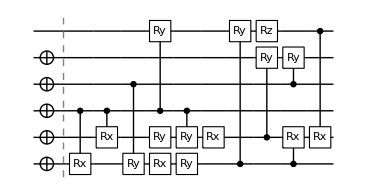

runtime=0.0382511 hours

nansatz=15

nansatz/cycle={0,15,15}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,3.89252×10^-8,3.89252×10^-8}

<E>=-5.76993

<E>-E_gs=3.89252×10^-8

Trial 2

Tue 8 Feb 2022 09:43:58GMT

target: -5.76993

@cycle1, fev:386, <E>: -5.76992697312104 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 5, 7, 14, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:562, <E>: -5.76992697312104 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 5, 7, 14, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:762, <E>: -5.76992697312104 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 5, 7, 14, 1}

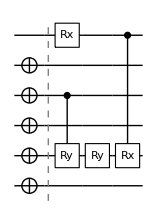

runtime=0.0207797 hours

nansatz=4

nansatz/cycle={0,4,4}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,1.14985×10^-9,1.14985×10^-9}

<E>=-5.76993

<E>-E_gs=1.14985×10^-9

Trial 3

Tue 8 Feb 2022 09:45:13GMT

target: -5.76993

@cycle1, fev:336, <E>: -5.769926951391987 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 12, 2}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:480, <E>: -5.769926951391987 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 12, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:695, <E>: -5.769926951391987 nansatz: 6 merged-smallθ-metric-bf-gmerged: {1, 11, 0, 12, 0}

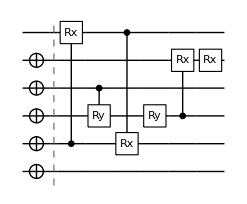

runtime=0.0189419 hours

nansatz=6

nansatz/cycle={0,6,6}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,2.28789×10^-8,2.28789×10^-8}

<E>=-5.76993

<E>-E_gs=2.28789×10^-8

Trial 4

Tue 8 Feb 2022 09:46:21GMT

target: -5.76993

@cycle1, fev:584, <E>: -5.769926883736781 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 8, 7, 10, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:697, <E>: -5.769926883736781 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 8, 7, 10, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:998, <E>: -5.769926883736781 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 8, 7, 10, 1}

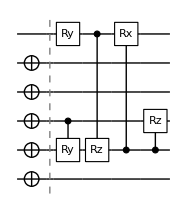

runtime=0.0255416 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,9.05341×10^-8,9.05341×10^-8}

<E>=-5.76993

<E>-E_gs=9.05341×10^-8

Trial 5

Tue 8 Feb 2022 09:47:53GMT

target: -5.76993

@cycle1, fev:370, <E>: -5.769926940898053 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 12, 9, 4, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:507, <E>: -5.769926940898053 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 12, 9, 4, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:829, <E>: -5.769926940898053 nansatz: 5 merged-smallθ-metric-bf-gmerged: {0, 12, 9, 4, 0}

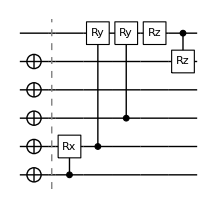

runtime=0.0221858 hours

nansatz=5

nansatz/cycle={0,5,5}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,3.33728×10^-8,3.33728×10^-8}

<E>=-5.76993

<E>-E_gs=3.33728×10^-8

Trial 6

Tue 8 Feb 2022 09:49:13GMT

target: -5.76993

@cycle1, fev:1175, <E>: -5.769926958418937 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 11, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:1383, <E>: -5.769926958418937 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 11, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1701, <E>: -5.769926958418937 nansatz: 13 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 11, 1}

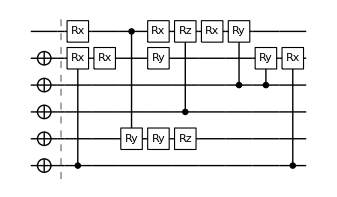

runtime=0.0442507 hours

nansatz=13

nansatz/cycle={0,13,13}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,1.58519×10^-8,1.58519×10^-8}

<E>=-5.76993

<E>-E_gs=1.58519×10^-8

Trial 7

Tue 8 Feb 2022 09:51:52GMT

target: -5.76993

@cycle1, fev:542, <E>: -5.769926931273126 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 16, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:840, <E>: -5.769926931273126 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 16, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:1061, <E>: -5.769926931273126 nansatz: 6 merged-smallθ-metric-bf-gmerged: {0, 6, 0, 16, 1}

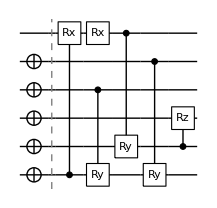

runtime=0.0286213 hours

nansatz=6

nansatz/cycle={0,6,6}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,4.29978×10^-8,4.29978×10^-8}

<E>=-5.76993

<E>-E_gs=4.29978×10^-8

Trial 8

Tue 8 Feb 2022 09:53:35GMT

target: -5.76993

@cycle1, fev:546, <E>: -5.769926974270846 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 6, 13, 2}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:686, <E>: -5.769926974270846 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 6, 13, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:926, <E>: -5.769926974270846 nansatz: 2 merged-smallθ-metric-bf-gmerged: {0, 9, 6, 13, 1}

-Graphics-

runtime=0.0214032 hours

nansatz=2

nansatz/cycle={0,2,2}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,3.90799×10^-14,3.90799×10^-14}

<E>=-5.76993

<E>-E_gs=3.90799×10^-14

Trial 9

Tue 8 Feb 2022 09:54:52GMT

target: -5.76993

@cycle1, fev:459, <E>: -5.76992658926146 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 7, 9, 0}

@cycle2, pathetic result.

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:633, <E>: -5.76992658926146 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 7, 9, 0}

@cycle3, pathetic result.

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:917, <E>: -5.76992658926146 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 7, 9, 1}

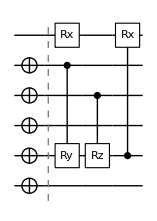

runtime=0.0254843 hours

nansatz=4

nansatz/cycle={0,4,4}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,3.85009×10^-7,3.84809×10^-7}

<E>=-5.76993

<E>-E_gs=3.84809×10^-7

Trial 10

Tue 8 Feb 2022 09:56:24GMT

target: -5.76993

@cycle1, fev:384, <E>: -5.7699269653142675 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 15, 0, 0}

I'm slowing down. Number of gates is increased to 24 @cycle 2

@cycle2, fev:566, <E>: -5.7699269653142675 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 15, 0, 0}

I'm slowing down. Number of gates is increased to 29 @cycle 3

@cycle3, fev:793, <E>: -5.7699269653142675 nansatz: 4 merged-smallθ-metric-bf-gmerged: {0, 9, 15, 0, 0}

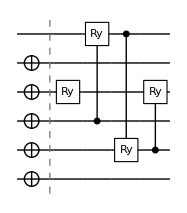

runtime=0.0214056 hours

nansatz=4

nansatz/cycle={0,4,4}

<E>/cycle={-5.76412,-5.76993,-5.76993}

ϵ/cycle={0.00580407,8.95662×10^-9,8.22264×10^-9}

<E>=-5.76993

<E>-E_gs=8.22264×10^-9

{-5.76993,-5.76993,-5.76993,-5.76993,-5.76993,-5.76993,-5.76993,-5.76993,-5.76993,-5.76993}

```mathematica
results={};
Table[
Print["Trial ",trial];
Print@Now;
Print["target: ",groundstate];
DestroyAllQuregs[];
conf=DefaultConfig[nqubits];
{timing,{Elist,ansatz,θvars,finmsg,ncycle,fev,aborted,cycleres,elim}}=AbsoluteTiming[VQEGS[nqubits,hamiltonian,conf]];

Print@DrawCircuit[{conf["ansatzinit"],ansatz},nqubits];
Print["runtime=",timing/3600," hours"];
Print["nansatz=",Length@ansatz];
Print["nansatz/cycle=",Length@#&/@cycleres["ansatz"]];
Print["<E>/cycle=",cycleres["E"]];
Print["ϵ/cycle=",cycleres["E"]-groundstate];
{ψ,ψwork}=CreateQuregs[nqubits,2];
ApplyCircuit[ψ,Join[conf["ansatzinit"],ansatz]/.θvars];
ecur=CalcExpecPauliSum[ψ,hamiltonian,ψwork];
Print["<E>=",ecur];
Print["<E>-E_gs=",ecur-groundstate];
DestroyAllQuregs[];
AppendTo[results,{ansatz,θvars,timing,cycleres,fev,aborted,elim}];
ecur
,{trial,10}]
```

## Total results

```mathematica
{ψ,ψwork}=CreateQuregs[nqubits,2];
ansatzinit=Table[Subscript[X, j],{j,0,4}];
chemacc=1.59*10^-3;
trial=1;
disp1=Table[
ApplyCircuit[InitZeroState@ψ,Join[ansatzinit,res⟦1⟧]/.res⟦2⟧];
ϵgs=CalcExpecPauliSum[ψ,hamiltonian,ψwork]-groundstate;
{trial++,
res⟦3⟧/60,
ϵgs<chemacc,
ϵgs,
Length@res⟦1⟧,
ToString[res⟦-1⟧],
ToString[res⟦-3⟧],
ToString[Length[#]&/@res⟦4⟧⟦"ansatz"⟧],
ToString[res⟦-2⟧]
}
,{res,results}];
PrependTo[disp1,{"trial","runtime(min)","chemacc?","ϵgs","ngates", "elims","fevs","ngates/pcycle","aborted cycle"}];
DestroyAllQuregs[]
```

```mathematica
disp1//TableForm
```

trial | runtime(min) | chemacc? | ϵgs | ngates | elims | fevs | ngates/pcycle | aborted cycle
1 | 2.29507 | True | 3.89252×10^-8 | 15 | {0, 9, 0, 6} | 1352 | {0, 15, 15} | {2, 3}
2 | 1.24678 | True | 1.14985×10^-9 | 4 | {0, 5, 7, 14} | 795 | {0, 4, 4} | {2, 3}
3 | 1.13652 | True | 2.28789×10^-8 | 6 | {1, 11, 0, 12} | 762 | {0, 6, 6} | {2, 3}
4 | 1.5325 | True | 9.05341×10^-8 | 5 | {0, 8, 7, 10} | 1071 | {0, 5, 5} | {}
5 | 1.33115 | True | 3.33728×10^-8 | 5 | {0, 12, 9, 4} | 915 | {0, 5, 5} | {2, 3}
6 | 2.65504 | True | 1.58519×10^-8 | 13 | {0, 6, 0, 11} | 1966 | {0, 13, 13} | {2, 3}
7 | 1.71728 | True | 4.29978×10^-8 | 6 | {0, 6, 0, 16} | 1120 | {0, 6, 6} | {2, 3}
8 | 1.28419 | True | 3.90799×10^-14 | 2 | {0, 9, 6, 13} | 1188 | {0, 2, 2} | {2, 3}
9 | 1.52906 | True | 3.84809×10^-7 | 4 | {0, 9, 7, 9} | 966 | {0, 4, 4} | {}
10 | 1.28434 | True | 8.22264×10^-9 | 4 | {0, 9, 15, 0} | 818 | {0, 4, 4} | {2, 3}

```mathematica
results
```

{{{C_2[Rx_0[θ_22]],C_2[Rx_1[θ_19]],C_3[Ry_0[θ_16]],Ry_1[θ_8],C_2[Ry_5[θ_23]],Rx_0[θ_14],C_2[Ry_1[θ_28]],Ry_0[θ_9],Rx_1[θ_5],C_0[Ry_5[θ_4]],C_1[Ry_4[θ_10]],Rz_5[θ_27],C_3[Ry_4[θ_29]],C_0[Rx_1[θ_12]],C_5[Rx_1[θ_18]]},<|θ_4→0.444915,θ_5→-0.007058,θ_8→-0.177929,θ_9→-0.22425,θ_10→0.031783,θ_12→-0.000851424,θ_14→0.148381,θ_16→0.226661,θ_18→3.14136,θ_19→0.00791282,θ_22→-0.14465,θ_23→-0.301445,θ_27→1.57033,θ_28→0.177929,θ_29→-0.0305044|>,137.704,<|ansatz→{{},{C_2[Rx_0[θ_22]],C_2[Rx_1[θ_19]],C_3[Ry_0[θ_16]],Ry_1[θ_8],C_2[Ry_5[θ_23]],Rx_0[θ_14],C_2[Ry_1[θ_28]],Ry_0[θ_9],Rx_1[θ_5],C_0[Ry_5[θ_4]],C_1[Ry_4[θ_10]],Rz_5[θ_27],C_3[Ry_4[θ_29]],C_0[Rx_1[θ_12]],C_5[Rx_1[θ_18]]},{C_2[Rx_0[θ_22]],C_2[Rx_1[θ_19]],C_3[Ry_0[θ_16]],Ry_1[θ_8],C_2[Ry_5[θ_23]],Rx_0[θ_14],C_2[Ry_1[θ_28]],Ry_0[θ_9],Rx_1[θ_5],C_0[Ry_5[θ_4]],C_1[Ry_4[θ_10]],Rz_5[θ_27],C_3[Ry_4[θ_29]],C_0[Rx_1[θ_12]],C_5[Rx_1[θ_18]]}},θvars→{<||>,<|θ_4→0.444915,θ_5→-0.007058,θ_8→-0.177929,θ_9→-0.22425,θ_10→0.031783,θ_12→-0.000851424,θ_14→0.148381,θ_16→0.226661,θ_18→3.14136,θ_19→0.00791282,θ_22→-0.14465,θ_23→-0.301445,θ_27→1.57033,θ_28→0.177929,θ_29→-0.0305044|>,<|θ_4→0.444915,θ_5→-0.007058,θ_8→-0.177929,θ_9→-0.22425,θ_10→0.031783,θ_12→-0.000851424,θ_14→0.148381,θ_16→0.226661,θ_18→3.14136,θ_19→0.00791282,θ_22→-0.14465,θ_23→-0.301445,θ_27→1.57033,θ_28→0.177929,θ_29→-0.0305044|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,1352,{2,3},{0,9,0,6}},{{C_3[Ry_1[θ_13]],Rx_5[θ_22],Ry_1[θ_19],C_5[Rx_1[θ_26]]},<|θ_13→-0.024646,θ_19→0.0246459,θ_22→-0.143525,θ_26→3.14167|>,74.8069,<|ansatz→{{},{C_3[Ry_1[θ_13]],Rx_5[θ_22],Ry_1[θ_19],C_5[Rx_1[θ_26]]},{C_3[Ry_1[θ_13]],Rx_5[θ_22],Ry_1[θ_19],C_5[Rx_1[θ_26]]}},θvars→{<||>,<|θ_13→-0.024646,θ_19→0.0246459,θ_22→-0.143525,θ_26→3.14167|>,<|θ_13→-0.024646,θ_19→0.0246459,θ_22→-0.143525,θ_26→3.14167|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,795,{2,3},{0,5,7,14}},{{C_1[Rx_5[θ_3]],C_3[Ry_2[θ_24]],C_5[Rx_1[θ_20]],Ry_2[θ_25],C_2[Rx_4[θ_26]],Rx_4[θ_29]},<|θ_3→-0.143379,θ_20→3.14159,θ_24→0.243163,θ_25→-0.243163,θ_26→0.0842325,θ_29→-0.085188|>,68.191,<|ansatz→{{},{C_1[Rx_5[θ_3]],C_3[Ry_2[θ_24]],C_5[Rx_1[θ_20]],Ry_2[θ_25],C_2[Rx_4[θ_26]],Rx_4[θ_29]},{C_1[Rx_5[θ_3]],C_3[Ry_2[θ_24]],C_5[Rx_1[θ_20]],Ry_2[θ_25],C_2[Rx_4[θ_26]],Rx_4[θ_29]}},θvars→{<||>,<|θ_3→-0.143379,θ_20→3.14159,θ_24→0.243163,θ_25→-0.243163,θ_26→0.0842325,θ_29→-0.085188|>,<|θ_3→-0.143379,θ_20→3.14159,θ_24→0.243163,θ_25→-0.243163,θ_26→0.0842325,θ_29→-0.085188|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,762,{2,3},{1,11,0,12}},{{C_2[Ry_1[θ_2]],Ry_5[θ_18],C_5[Rz_1[θ_16]],C_1[Rx_5[θ_10]],C_1[Rz_2[θ_15]]},<|θ_2→0.143128,θ_10→3.14139,θ_15→3.425,θ_16→3.0031,θ_18→3.14139|>,91.9499,<|ansatz→{{},{C_2[Ry_1[θ_2]],Ry_5[θ_18],C_5[Rz_1[θ_16]],C_1[Rx_5[θ_10]],C_1[Rz_2[θ_15]]},{C_2[Ry_1[θ_2]],Ry_5[θ_18],C_5[Rz_1[θ_16]],C_1[Rx_5[θ_10]],C_1[Rz_2[θ_15]]}},θvars→{<||>,<|θ_2→0.143128,θ_10→3.14139,θ_15→3.425,θ_16→3.0031,θ_18→3.14139|>,<|θ_2→0.143128,θ_10→3.14139,θ_15→3.425,θ_16→3.0031,θ_18→3.14139|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,1071,{},{0,8,7,10}},{{C_0[Rx_1[θ_25]],C_1[Ry_5[θ_22]],C_2[Ry_5[θ_23]],Rz_5[θ_1],C_5[Rz_4[θ_27]]},<|θ_1→-0.321342,θ_22→3.1416,θ_23→-3.1416,θ_25→0.143323,θ_27→-2.50331|>,79.869,<|ansatz→{{},{C_0[Rx_1[θ_25]],C_1[Ry_5[θ_22]],C_2[Ry_5[θ_23]],Rz_5[θ_1],C_5[Rz_4[θ_27]]},{C_0[Rx_1[θ_25]],C_1[Ry_5[θ_22]],C_2[Ry_5[θ_23]],Rz_5[θ_1],C_5[Rz_4[θ_27]]}},θvars→{<||>,<|θ_1→-0.321342,θ_22→3.1416,θ_23→-3.1416,θ_25→0.143323,θ_27→-2.50331|>,<|θ_1→-0.321342,θ_22→3.1416,θ_23→-3.1416,θ_25→0.143323,θ_27→-2.50331|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,915,{2,3},{0,12,9,4}},{{C_0[Rx_4[θ_7]],Rx_5[θ_3],Rx_4[θ_12],C_5[Ry_1[θ_8]],Ry_4[θ_18],Ry_1[θ_9],Rx_5[θ_16],C_2[Rz_5[θ_17]],Rz_1[θ_24],Rx_5[θ_21],C_3[Ry_5[θ_25]],C_3[Ry_4[θ_28]],C_0[Rx_4[θ_29]]},<|θ_3→-0.342823,θ_7→-0.0827007,θ_8→-0.879846,θ_9→0.0226069,θ_12→-0.34427,θ_16→-0.371287,θ_17→-1.71676,θ_18→-0.113461,θ_21→-0.117926,θ_24→-0.188315,θ_25→-0.675032,θ_28→0.113369,θ_29→0.426996|>,159.302,<|ansatz→{{},{C_0[Rx_4[θ_7]],Rx_5[θ_3],Rx_4[θ_12],C_5[Ry_1[θ_8]],Ry_4[θ_18],Ry_1[θ_9],Rx_5[θ_16],C_2[Rz_5[θ_17]],Rz_1[θ_24],Rx_5[θ_21],C_3[Ry_5[θ_25]],C_3[Ry_4[θ_28]],C_0[Rx_4[θ_29]]},{C_0[Rx_4[θ_7]],Rx_5[θ_3],Rx_4[θ_12],C_5[Ry_1[θ_8]],Ry_4[θ_18],Ry_1[θ_9],Rx_5[θ_16],C_2[Rz_5[θ_17]],Rz_1[θ_24],Rx_5[θ_21],C_3[Ry_5[θ_25]],C_3[Ry_4[θ_28]],C_0[Rx_4[θ_29]]}},θvars→{<||>,<|θ_3→-0.342823,θ_7→-0.0827007,θ_8→-0.879846,θ_9→0.0226069,θ_12→-0.34427,θ_16→-0.371287,θ_17→-1.71676,θ_18→-0.113461,θ_21→-0.117926,θ_24→-0.188315,θ_25→-0.675032,θ_28→0.113369,θ_29→0.426996|>,<|θ_3→-0.342823,θ_7→-0.0827007,θ_8→-0.879846,θ_9→0.0226069,θ_12→-0.34427,θ_16→-0.371287,θ_17→-1.71676,θ_18→-0.113461,θ_21→-0.117926,θ_24→-0.188315,θ_25→-0.675032,θ_28→0.113369,θ_29→0.426996|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,1966,{2,3},{0,6,0,11}},{{C_0[Rx_5[θ_29]],Rx_5[θ_27],C_3[Ry_0[θ_4]],C_5[Ry_1[θ_9]],C_4[Ry_0[θ_24]],C_1[Rz_2[θ_13]]},<|θ_4→0.0639492,θ_9→3.14231,θ_13→3.14159,θ_24→-0.0635556,θ_27→-0.32415,θ_29→0.467698|>,103.037,<|ansatz→{{},{C_0[Rx_5[θ_29]],Rx_5[θ_27],C_3[Ry_0[θ_4]],C_5[Ry_1[θ_9]],C_4[Ry_0[θ_24]],C_1[Rz_2[θ_13]]},{C_0[Rx_5[θ_29]],Rx_5[θ_27],C_3[Ry_0[θ_4]],C_5[Ry_1[θ_9]],C_4[Ry_0[θ_24]],C_1[Rz_2[θ_13]]}},θvars→{<||>,<|θ_4→0.0639492,θ_9→3.14231,θ_13→3.14159,θ_24→-0.0635556,θ_27→-0.32415,θ_29→0.467698|>,<|θ_4→0.0639492,θ_9→3.14231,θ_13→3.14159,θ_24→-0.0635556,θ_27→-0.32415,θ_29→0.467698|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,1120,{2,3},{0,6,0,16}},{{C_3[Rx_5[θ_2]],C_5[Rx_1[θ_17]]},<|θ_2→-0.143461,θ_17→3.1416|>,77.0516,<|ansatz→{{},{C_3[Rx_5[θ_2]],C_5[Rx_1[θ_17]]},{C_3[Rx_5[θ_2]],C_5[Rx_1[θ_17]]}},θvars→{<||>,<|θ_2→-0.143461,θ_17→3.1416|>,<|θ_2→-0.143461,θ_17→3.1416|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,1188,{2,3},{0,9,6,13}},{{Rx_5[θ_10],C_4[Ry_1[θ_6]],C_3[Rz_1[θ_27]],C_1[Rx_5[θ_23]]},<|θ_6→-0.144627,θ_10→-3.14159,θ_23→3.14159,θ_27→1.5705|>,91.7435,<|ansatz→{{},{Rx_5[θ_10],C_4[Ry_1[θ_6]],C_3[Rz_1[θ_27]],C_1[Rx_5[θ_23]]},{Rx_5[θ_10],C_4[Ry_1[θ_6]],C_3[Rz_1[θ_27]],C_1[Rx_5[θ_23]]}},θvars→{<||>,<|θ_6→-0.144627,θ_10→-3.14159,θ_23→3.14159,θ_27→1.57039|>,<|θ_6→-0.144627,θ_10→-3.14159,θ_23→3.14159,θ_27→1.5705|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,966,{},{0,9,7,9}},{{Ry_3[θ_13],C_2[Ry_5[θ_21]],C_5[Ry_1[θ_14]],C_1[Ry_3[θ_11]]},<|θ_11→-0.00186711,θ_13→0.00184883,θ_14→3.14136,θ_21→-0.143435|>,77.0602,<|ansatz→{{},{Ry_3[θ_13],C_2[Ry_5[θ_21]],C_5[Ry_1[θ_14]],C_1[Ry_3[θ_11]]},{Ry_3[θ_13],C_2[Ry_5[θ_21]],C_5[Ry_1[θ_14]],C_1[Ry_3[θ_11]]}},θvars→{<||>,<|θ_11→-0.0018792,θ_13→0.0017987,θ_14→3.14193,θ_21→-0.143454|>,<|θ_11→-0.00186711,θ_13→0.00184883,θ_14→3.14136,θ_21→-0.143435|>},E→{-5.76412,-5.76993,-5.76993},idx→{1,31,31}|>,818,{2,3},{0,9,15,0}}}